```mathematica
Полученные ур-я движения для квадрупольного возмущения из ноутбука eqA,eqB;
```

```mathematica
Jastr=( b  h1 Sin[ϕa+ϕb]+a(Cos[2ϕa]h121+h122 Sin[2ϕa])+b(Cos[ϕa-ϕb]h131+h132 Sin[ϕa-ϕb])) 2a/.{a->Sqrt[Ja],b->Sqrt[Jb]};
Jbstr=(b  (h2 Sin[2ϕb])+a(Cos[ϕb+ϕb]h221+h222 Sin[ϕa+ϕb])+a(Cos[ϕa-ϕb]h231+h232 Sin[ϕa-ϕb])) 2b/.{a->Sqrt[Ja],b->Sqrt[Jb]};
ϕastr=(h12+ Cos[2ϕa]h1+b(Cos[ϕa+ϕb]h122-h121 Sin[ϕa+ϕb])/a+b(Cos[ϕa-ϕb]h132-h131 Sin[ϕa-ϕb])/a+na+1/2+Δ+δ)/.{a->Sqrt[Ja],b->Sqrt[Jb]};
ϕbstr=(h22+ Cos[2ϕb]h2+a(Cos[ϕa+ϕb]h222-h221 Sin[ϕa+ϕb])/b+a(Cos[ϕa-ϕb]h232-h231 Sin[ϕa-ϕb])/b+nb+1/2+Δ-δ)/.{a->Sqrt[Ja],b->Sqrt[Jb]};
```

```mathematica
_______для дифуров;
```

```mathematica
Jastrd=Jastr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
Jbstrd=Jbstr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
ϕastrd=ϕastr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
ϕbstrd=ϕbstr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
```

```mathematica
_______получение гамильтониана;
```

```mathematica
Simplify[Integrate[Jastr,ϕa]]
```

2 √Ja (h11 ϕa-1/2 h1 √Ja Cos[2 ϕa]-h132 √Jb Cos[ϕa-ϕb]-h122 √Jb Cos[ϕa+ϕb]+h131 √Jb Sin[ϕa-ϕb]+h121 √Jb Sin[ϕa+ϕb])

```mathematica
Simplify[Integrate[ϕastr,Ja]]
```

Ja/2+h12 Ja+Ja na+Ja δ+Ja Δ+h1 Ja Cos[2 ϕa]+2 √Ja √Jb (h132 Cos[ϕa-ϕb]-h131 Sin[ϕa-ϕb])+2 √Ja √Jb (h122 Cos[ϕa+ϕb]-h121 Sin[ϕa+ϕb])

```mathematica
Simplify[Integrate[ϕbstr,Jb]]
```

Jb/2+h22 Jb+Jb nb-Jb δ+Jb Δ+h2 Jb Cos[2 ϕb]+2 √Ja √Jb (h232 Cos[ϕa-ϕb]-h231 Sin[ϕa-ϕb])+2 √Ja √Jb (h222 Cos[ϕa+ϕb]-h221 Sin[ϕa+ϕb])

```mathematica
H=Simplify[Ja/2+h12 Ja+Ja na+Ja δ+Ja Δ+h1 Ja Cos[2 ϕa]+Jb/2+h22 Jb+Jb nb-Jb δ+Jb Δ+h2 Jb Cos[2 ϕb]+2 √Ja √Jb (h132 Cos[ϕa-ϕb]-h131 Sin[ϕa-ϕb])+2 √Ja √Jb (h122 Cos[ϕa+ϕb]-h121 Sin[ϕa+ϕb])+2 √Ja h11 ϕa+ 2 √Jb h21 ϕb]
```

Ja/2+h12 Ja+Jb/2+h22 Jb+Ja na+Jb nb+Ja δ-Jb δ+Ja Δ+Jb Δ+2 h11 √Ja ϕa+2 h21 √Jb ϕb+h1 Ja Cos[2 ϕa]+h2 Jb Cos[2 ϕb]+2 √Ja √Jb (h132 Cos[ϕa-ϕb]-h131 Sin[ϕa-ϕb])+2 √Ja √Jb (h122 Cos[ϕa+ϕb]-h121 Sin[ϕa+ϕb])

```mathematica
Simplify[H/.{ϕa->ϕs-ϕd,ϕb->ϕs+ϕd}]
```

Ja/2+h12 Ja+Jb/2+h22 Jb+Ja na+Jb nb+Ja δ-Jb δ+Ja Δ+Jb Δ+2 h11 √Ja (-ϕd+ϕs)+2 h21 √Jb (ϕd+ϕs)+h1 Ja Cos[2 (ϕd-ϕs)]+h2 Jb Cos[2 (ϕd+ϕs)]+2 √Ja √Jb (h132 Cos[2 ϕd]+h131 Sin[2 ϕd])+2 √Ja √Jb (h122 Cos[2 ϕs]-h121 Sin[2 ϕs])

```mathematica
{Ja'[t]==Jastrd,Jb'[t]==Jbstrd,ϕa'[t]==ϕastrd,ϕb'[t]==ϕbstrd,Ja[0]==0.8,Jb[0]==0.8,ϕa[0]==0,ϕb[0]==0}/.{h11->1,h12->.5,h21->1,h22->.5,h1->-1,h2->0,h131->0,h132->0,h121->0,h122->1,h211->0,na->2,nb->4,Δ->0,δ->0.01}
```

{Ja'[t]==2 √Ja[t] (1-√Ja[t] Sin[2 ϕa[t]]+√Jb[t] Sin[ϕa[t]+ϕb[t]]),Jb'[t]==2 √Jb[t] (1+√Ja[t] (h231 Cos[ϕa[t]-ϕb[t]]+h232 Sin[ϕa[t]-ϕb[t]])+√Ja[t] (h221 Cos[2 ϕb[t]]+h222 Sin[ϕa[t]+ϕb[t]])),ϕa'[t]==3.01-Cos[2 ϕa[t]]+(Cos[ϕa[t]+ϕb[t]] √Jb[t])/(√Ja[t]),ϕb'[t]==4.99+(√Ja[t] (h232 Cos[ϕa[t]-ϕb[t]]-h231 Sin[ϕa[t]-ϕb[t]]))/(√Jb[t])+(√Ja[t] (h222 Cos[ϕa[t]+ϕb[t]]-h221 Sin[ϕa[t]+ϕb[t]]))/(√Jb[t]),Ja[0]==0.8,Jb[0]==0.8,ϕa[0]==0,ϕb[0]==0}

$Aborted

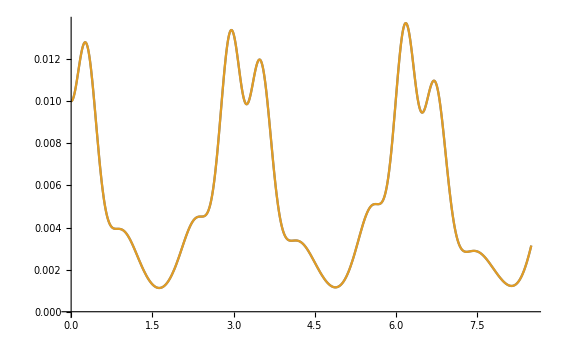

```mathematica
s=NDSolve[{Ja'[t]==Jastrd,Jb'[t]==Jbstrd,ϕa'[t]==ϕastrd,ϕb'[t]==ϕbstrd,Ja[0]==.01,Jb[0]==.01,ϕa[0]==0,ϕb[0]==0}/.{h11->0,h12->.5,h21->0,h22->.5,h1->1,h2->1,h121->0,h122->1,h221->0,h222->1,h131->0,h132->1,h231->0,h232->1,na->2,nb->4,Δ->0,δ->0.01},{Ja[t],ϕa[t],Jb[t],ϕb[t]},{t,0,8.5}];
Plot[Evaluate[{Ja[t],Jb[t]}/.s,{t,0,8.5}]]
```

```mathematica
отсутствие соленоидов;
Jastr=(b h1(Sin[ϕa+ϕb]+ Sin[ϕa-ϕb])) 2a/.{a->Sqrt[Ja],b->Sqrt[Jb]};
Jbstr=(a h1(Sin[ϕa+ϕb]+ Sin[ϕa-ϕb]))2b/.{a->Sqrt[Ja],b->Sqrt[Jb]};
ϕastr=(b h1(Cos[ϕa+ϕb]+ Cos[ϕa-ϕb])/a+na+1/2+Δ+δ)/.{a->Sqrt[Ja],b->Sqrt[Jb]};
ϕbstr=(a h1(Cos[ϕa+ϕb]+ Cos[ϕa-ϕb])/b+nb+1/2+Δ-δ)/.{a->Sqrt[Ja],b->Sqrt[Jb]};
_______для дифуров;
Jastrd=Jastr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
Jbstrd=Jbstr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
ϕastrd=ϕastr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
ϕbstrd=ϕbstr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
_______получение гамильтониана;
```

```mathematica
Simplify[Integrate[Jastr,ϕa]]
```

-4 h1 √Ja √Jb Cos[ϕa] Cos[ϕb]

```mathematica
Simplify[Integrate[ϕastr,Ja]]
```

Ja (1/3+na+δ+Δ)+4 h1 √Ja √Jb Cos[ϕa] Cos[ϕb]

```mathematica
Simplify[Integrate[ϕbstr,Jb]]
```

Jb/3+Jb nb-Jb δ+Jb Δ+4 h1 √Ja √Jb Cos[ϕa] Cos[ϕb]

```mathematica
H=FullSimplify[Ja (1/2+na+δ+Δ)+4 h1 √Ja √Jb Cos[ϕa] Cos[ϕb]+Jb/2+Jb nb-Jb δ+Jb Δ]
```

Jb (1/2+nb)+Jb (-δ+Δ)+Ja (1/2+na+δ+Δ)+4 h1 √Ja √Jb Cos[ϕa] Cos[ϕb]

```mathematica
{Ja'[t]==Jastrd,Jb'[t]==Jbstrd,ϕa'[t]==ϕastrd,ϕb'[t]==ϕbstrd}/.{h1->-1,na->2,nb->4,Δ->0,δ->0.01}
```

{Ja'[t]==-2 √Ja[t] √Jb[t] (Sin[ϕa[t]-ϕb[t]]+Sin[ϕa[t]+ϕb[t]]),Jb'[t]==-2 √Ja[t] √Jb[t] (Sin[ϕa[t]-ϕb[t]]+Sin[ϕa[t]+ϕb[t]]),ϕa'[t]==2.51-((Cos[ϕa[t]-ϕb[t]]+Cos[ϕa[t]+ϕb[t]]) √Jb[t])/(√Ja[t]),ϕb'[t]==4.49-((Cos[ϕa[t]-ϕb[t]]+Cos[ϕa[t]+ϕb[t]]) √Ja[t])/(√Jb[t])}

```mathematica
,Jb'[t]==Jbstrd,ϕa'[t]==ϕastrd,ϕb'[t]==ϕbstrd,ϕa[t],Jb[t],ϕb[t]
```

```mathematica
s=DSolve[{Ja'[t]==Jastrd,Jb'[t]==Jbstrd,ϕa'[t]==ϕastrd,ϕb'[t]==ϕbstrd}/.{h1->-1,na->2,nb->4,Δ->0,δ->0.01},{Ja[t],ϕa[t],Jb[t],ϕb[t]},t]
```

DSolve[{Ja'[t]==-2 √Ja[t] √Jb[t] (Sin[ϕa[t]-ϕb[t]]+Sin[ϕa[t]+ϕb[t]]),Jb'[t]==-2 √Ja[t] √Jb[t] (Sin[ϕa[t]-ϕb[t]]+Sin[ϕa[t]+ϕb[t]]),ϕa'[t]==2.51-((Cos[ϕa[t]-ϕb[t]]+Cos[ϕa[t]+ϕb[t]]) √Jb[t])/(√Ja[t]),ϕb'[t]==4.49-((Cos[ϕa[t]-ϕb[t]]+Cos[ϕa[t]+ϕb[t]]) √Ja[t])/(√Jb[t])},{Ja[t],ϕa[t],Jb[t],ϕb[t]},t]

```mathematica
s=DSolve[{Ja'[t]==15t,Jb'[t]==t^2,ϕa'[t]==-2Ja[t],ϕb'[t]==1}/.{h1->-1,na->2,nb->4,Δ->0,δ->0.01},{Ja[t],ϕa[t],Jb[t],ϕb[t]},t]
```

{{Ja[t]→(15 t^2)/2+C[1],ϕa[t]→-5 t^3-2 t C[1]+C[2],Jb[t]→t^3/3+C[3],ϕb[t]→t+C[4]}}

```mathematica
a[t] Exp[I ϕa[t]]==I b[t](Exp[I(ϕa[t]+ϕb[t])]+Exp[I(ϕa[t]-ϕb[t])]);
b[t] Exp[I ϕb[t]]==I a[t]( Exp[I(ϕa[t]+ϕb[t])]+Exp[I(ϕa[t]-ϕb[t])]);
```

```mathematica
Astrd=Astr/.{a->a[t],b->b[t],ϕa->ϕa[t],ϕb->ϕb[t]};
Bstrd=Bstr/.{a->a[t],b->b[t],ϕa->ϕa[t],ϕb->ϕb[t]};
```

```mathematica
s=DSolve[{D[a[t] Exp[I ϕa[t]],t]==I b[t](Exp[I(ϕa[t]+ϕb[t])]+Exp[I(ϕa[t]-ϕb[t])]),D[b[t] Exp[I ϕb[t]],t]==I a[t]( Exp[I(ϕa[t]+ϕb[t])]+Exp[I(ϕa[t]-ϕb[t])])},{a[t],ϕa[t],b[t],ϕb[t]},t]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[{ⅇ^(ⅈ ϕa[t]) a'[t]+ⅈ ⅇ^(ⅈ ϕa[t]) a[t] ϕa'[t]==ⅈ (ⅇ^(ⅈ (ϕa[t]-ϕb[t]))+ⅇ^(ⅈ (ϕa[t]+ϕb[t]))) b[t],ⅇ^(ⅈ ϕb[t]) b'[t]+ⅈ ⅇ^(ⅈ ϕb[t]) b[t] ϕb'[t]==ⅈ (ⅇ^(ⅈ (ϕa[t]-ϕb[t]))+ⅇ^(ⅈ (ϕa[t]+ϕb[t]))) a[t]},{a[t],ϕa[t],b[t],ϕb[t]},t]

```mathematica
Plot[Evaluate[{Ja[t],Jb[t]}/.s,{t,0,10}]]
```

```mathematica
Simplify[{Jastr== 0 ,Jbstr==0,ϕbstr==0,ϕastr==0}/.{h1->-1,na->0,nb->0,Δ->0}]
```

{√Ja √Jb Cos[ϕb] Sin[ϕa]==0,√Ja √Jb Cos[ϕb] Sin[ϕa]==0,2 δ+(4 √Ja Cos[ϕa] Cos[ϕb])/(√Jb)==1,1+2 δ==(4 √Jb Cos[ϕa] Cos[ϕb])/(√Ja)}

```mathematica
sol =Flatten[Solve[{Jastr== 0 ,Jbstr==0,ϕbstr==0,ϕastr==0}/.{h1->-1,na->0,nb->0} ,{Ja,Jb,ϕa,ϕb}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→0,ϕb→-ArcCos[-1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→0,ϕb→ArcCos[-1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→0,ϕb→-ArcCos[1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→0,ϕb→ArcCos[1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→-π,ϕb→-ArcCos[-1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→-π,ϕb→ArcCos[-1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→-π,ϕb→-ArcCos[1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→-π,ϕb→ArcCos[1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→π,ϕb→-ArcCos[-1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→π,ϕb→ArcCos[-1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→π,ϕb→-ArcCos[1/4 √(1-4 δ^2+4 Δ+4 Δ^2)],Jb→(-Ja-2 Ja δ-2 Ja Δ)/(-1+2 δ-2 Δ),ϕa→π,ϕb→ArcCos[1/4 √(1-4 δ^2+4 Δ+4 Δ^2)]}

```mathematica
(Jb/.sol)/.{Δ->Δ1,Ja->1}
```

(-5-2 δ-2 Δ1)/(-9+2 δ-2 Δ1)

```mathematica
Manipulate[Plot[(Jb/.sol)/.{Δ->Δ1,Ja->1},{δ,-0.5,0.5}],{Δ1,-0.5,0.5}]
```